# Generalized QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Resonant_k\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

## Grid

```mathematica
radius=2;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{20069,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{mat, d, idx, matEven, matOdd, esEven, esOdd,
          phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,
          fullVecsEven, fullVecsOdd},
    mat = Floqsym[jParam, alphaParam, kParam];
    d = 2 jParam + 1;
    idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];
    idxE = Ordering[phEven]; idxO = Ordering[phOdd];
    vecsEven = esEven[[2, idxE]];
    vecsOdd  = esOdd[[2, idxO]];
    fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];
    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];
    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ];
```

## Method

```mathematica
(*Floquet parameters*)
J=500;
d=2 J+1;
α=Pi/2.;
k=J*Pi(8/2.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 20069 points...

```mathematica
Print["Computing Floquet matrix..."];
data=GetQKTParityEigensystem[J,α,k];
```

Computing Floquet matrix...

```mathematica
neweigenvec=Join[data["Even","FullVectors"],data["Odd","FullVectors"]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

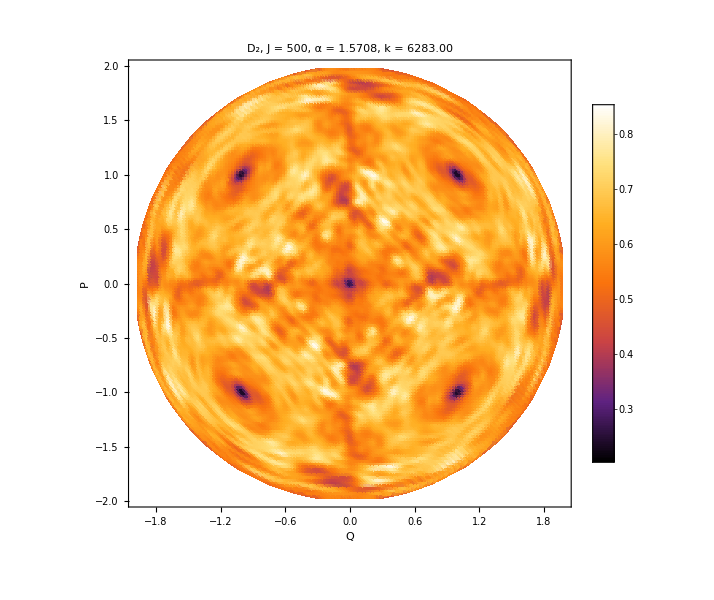

d2_J_500alpha_1.5708_k_6283.19_.png

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
Export["d2_J_"<>ToString[J]<>"alpha_"<>ToString[α]<>"_k_"<>ToString[k]<>"_.png",plot]
```

## Husimis

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,1,2J+1,100}];
```

## Husimis of degenerate groups

```mathematica
(* Operates on a single sector's phase list; returns indices local to that sector *)
GroupStateIndicesSector[phases_, delta_ : 0.01] :=
  Module[{ord, sp, n, breaks, starts, ends, slices},
    ord = Ordering[phases];
    sp  = phases[[ord]];
    n   = Length[sp];
    breaks = Select[Range[n - 1], sp[[# + 1]] - sp[[#]] > delta &];
    starts = Prepend[breaks + 1, 1];
    ends   = Append[breaks, n];
    slices = MapThread[Range, {starts, ends}];
    If[2 Pi - sp[[n]] + sp[[1]] < delta,
      slices = Prepend[slices[[2 ;; -2]], Join[slices[[-1]], slices[[1]]]]];
    ord[[#]] & /@ slices];

(* Splits the merged husimiValues matrix by parity sector *)
SectorHusimiValues[data_, husimiValues_] :=
  Module[{nEven = Length[data["Even"]["FullVectors"]]},
    <|"Even" -> husimiValues[[1 ;; nEven]],
      "Odd"  -> husimiValues[[nEven + 1 ;; All]]|>];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiSectors=SectorHusimiValues[data,husimiValues];
groupIndices=<|"Even"->GroupStateIndicesSector[data["Even"]["Phases"],0.1],"Odd"->GroupStateIndicesSector[data["Odd"]["Phases"],0.1]|>;
```

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
Do[Do[Module[{groupDir},groupDir=FileNameJoin[{dir,sector,"Group_"<>ToString[g]}];
If[!DirectoryQ[groupDir],CreateDirectory[groupDir]];
Do[Module[{idx,husimiList,plot},idx=groupIndices[sector][[g,i]];
husimiList=MapThread[Append,{region,husimiSectors[sector][[idx]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", "<>sector<>" Group "<>ToString[g]<>" ("<>ToString[Length[groupIndices[sector][[g]]]]<>" states)"<>", State "<>ToString[idx],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{groupDir,"Husimi_"<>sector<>"_state_"<>ToString[idx]<>".png"}],plot]],{i,Length[groupIndices[sector][[g]]]}]],{g,Length[groupIndices[sector]]}],{sector,{"Even","Odd"}}];
```

$Aborted

# Sortings

```mathematica
(* ── Quasienergies (both parities, same order as neweigenvec) ── *)
quasienergies = Join[data["Even", "Phases"], data["Odd", "Phases"]];

(* ── Husimi values: rows = eigenstates, cols = phase-space points ── *)
husimi = Abs[overlaps]^2;  (* already normalized per row *)

(* ── 1. IPR of each eigenstate over phase space ── *)
iprEigen = Total[husimi^2, {2}];

(* ── 2. Shannon entropy of each eigenstate ── *)
shannonEntropy = -Total[husimi * Log[husimi + $MachineEpsilon], {2}];
```

```mathematica
(* ── 3. Second moment (variance) of Husimi on phase space ── *)
Q = region[[All, 1]];
P = region[[All, 2]];
meanQ = husimi . Q;
meanP = husimi . P;
meanQ2 = husimi . (Q^2);
meanP2 = husimi . (P^2);
secondMoment = (meanQ2 - meanQ^2) + (meanP2 - meanP^2);
```

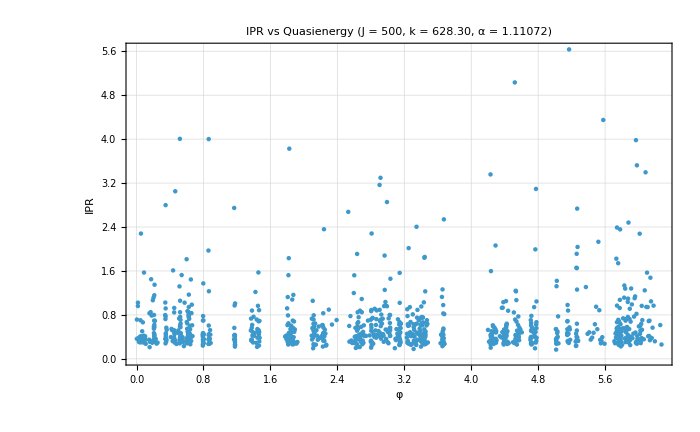

```mathematica
p1 = ListPlot[
  Transpose[{quasienergies, iprEigen}],
  FrameLabel -> {Style["φ", 16], Style["IPR", 16]},  PlotLabel -> Style["IPR vs Quasienergy  (J = " <> ToString[J] <> ", k = " <> ToString[NumberForm[k, {4,2}]] <> ", α = " <> ToString[N[α]] <> ")", 14],PlotTheme->"Detailed",PlotRange->All,ImageSize->700]
```

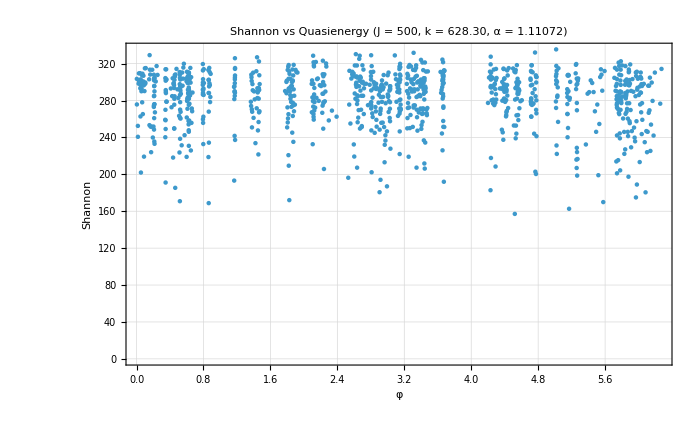

```mathematica
p2 = ListPlot[
  Transpose[{quasienergies, shannonEntropy}],
  FrameLabel -> {Style["φ", 16], Style["Shannon", 16]},  PlotLabel -> Style["Shannon vs Quasienergy  (J = " <> ToString[J] <> ", k = " <> ToString[NumberForm[k, {4,2}]] <> ", α = " <> ToString[N[α]] <> ")", 14],PlotTheme->"Detailed",PlotRange->All,ImageSize->700]
```

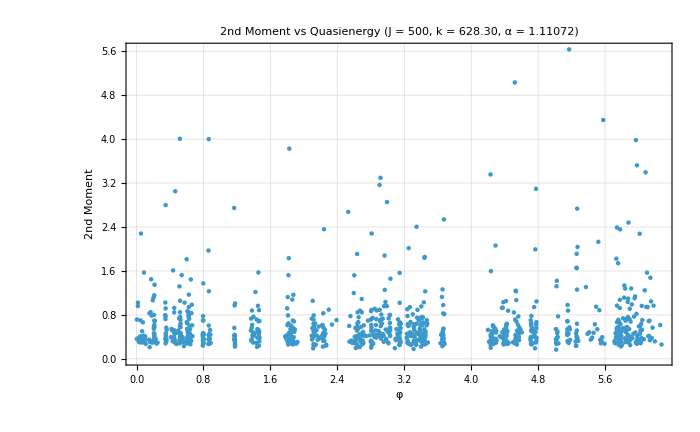

```mathematica
p1 = ListPlot[
  Transpose[{quasienergies, iprEigen}],
  FrameLabel -> {Style["φ", 16], Style["2nd Moment", 16]},  PlotLabel -> Style["2nd Moment vs Quasienergy  (J = " <> ToString[J] <> ", k = " <> ToString[NumberForm[k, {4,2}]] <> ", α = " <> ToString[N[α]] <> ")", 14],PlotTheme->"Detailed",PlotRange->All,ImageSize->700]
```

```mathematica
(* ── Composite localization score (rank each criterion, sum ranks) ── *)
rankIPR     = Ordering[Ordering[-iprEigen]];      (* high IPR = more localized -> rank ascending by -IPR *)
rankEntropy = Ordering[Ordering[shannonEntropy]];  (* low entropy = more localized -> rank ascending *)
rankMoment  = Ordering[Ordering[secondMoment]];   (* low moment = more localized -> rank ascending *)
compositeRank = rankIPR + rankEntropy + rankMoment;
```

```mathematica
nPlot = 50;
sortedIdx = Ordering[compositeRank];
selectedIdx = Take[sortedIdx, nPlot];

dir = "HusimiSorted";
If[!DirectoryQ[dir], CreateDirectory[dir]];

(* ── Distribute shared data to all kernels ── *)
DistributeDefinitions[region, husimi, quasienergies, shannonEntropy, iprEigen, selectedIdx, dir, nPlot];
```

```mathematica
ParallelDo[
  Module[{idx, husimiList, plot, fname},
    idx = selectedIdx[[n]];
    husimiList = MapThread[Append, {region, husimi[[idx]]}];
    plot = ListDensityPlot[husimiList,
      PlotRange -> All,
      PlotTheme -> "Detailed",
      ColorFunction -> "BlueGreenYellow",
      InterpolationOrder -> 1,
      AspectRatio -> 1,
      ImageSize -> 800,
      Frame -> True,
      FrameLabel -> {Style["Q", 30, Black], Rotate[Style["P", 30, Black], -90 Degree]},
      LabelStyle -> Directive[20, Black],
      PlotLabel -> Style[
        "rank=" <> ToString[n] <>
        "  q = " <> ToString[idx] <>
        "  φ = " <> ToString[NumberForm[quasienergies[[idx]], {5,3}]] <>
        "  S = " <> ToString[NumberForm[shannonEntropy[[idx]], {5,3}]] <>
        "  IPR = " <> ToString[NumberForm[iprEigen[[idx]], {4,3}]],
        18, Black]
    ];
    fname = FileNameJoin[{dir,
      "rank" <> IntegerString[n, 10, 3] <>
      "_q" <> ToString[idx] <>
      "_phi" <> ToString[NumberForm[quasienergies[[idx]], {5,3}]] <>
      ".png"}];
    Export[fname, plot];
  ],
  {n, 1, nPlot},
  Method -> "CoarsestGrained"
];
```

## Quasienergies

```mathematica
s = 5;
targets = Table[p * Pi / s, {p, 0, 2s - 1}];

(* wrap distance accounting for 2π periodicity *)
delta = Map[
  Min[Min[Abs[# - targets]], Min[Abs[# - targets - 2Pi]], Min[Abs[# - targets + 2Pi]]] &,
  quasienergies
];
```

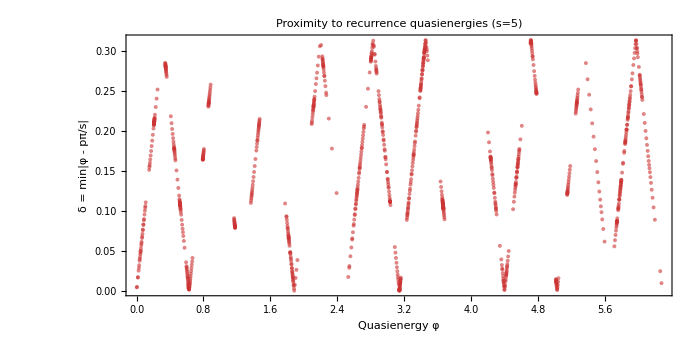

```mathematica
ListPlot[Transpose[{quasienergies,delta}],PlotStyle->Directive[PointSize[0.004],Opacity[0.6],RGBColor[0.8,0.2,0.2]],FrameLabel->{Style["Quasienergy φ",16],Style["δ = min|φ - pπ/s|",16]},PlotLabel->Style["Proximity to recurrence quasienergies  (s="<>ToString[s]<>")",14],LabelStyle->Directive[14,Black],ImageSize->700,AspectRatio->1/2,Frame->True]
```

```mathematica
thresholds={0.005,0.05,0.10,0.15};
Table[{thresh,Count[delta,d_/;d<thresh]},{thresh,thresholds}]//TableForm
```

0.005 | 43
0.05 | 181
0.1 | 288
0.15 | 497

```mathematica
(* ── Select eigenstates with delta < 0.02 (yields 60 states) ── *)
selectedIdx = Flatten[Position[delta, d_ /; d < 0.005]];

nPlot = Length[selectedIdx];  (* should be 60 *)
Print["Selected ", nPlot, " eigenstates with δ < 0.02"];

(* ── Sort selected by delta ascending within the selection ── *)
selectedIdx = selectedIdx[[Ordering[delta[[selectedIdx]]]]];

(* ── Export ── *)
dir = "HusimiDelta002";
If[!DirectoryQ[dir], CreateDirectory[dir]];

DistributeDefinitions[region, husimi, quasienergies, shannonEntropy, iprEigen, delta, selectedIdx, dir, nPlot];
```

Selected 43 eigenstates with δ < 0.02

```mathematica
ParallelDo[
  Module[{idx, husimiList, plot, fname},
    idx = selectedIdx[[n]];
    husimiList = MapThread[Append, {region, husimi[[idx]]}];
    plot = ListDensityPlot[husimiList,
      PlotRange -> All,
      PlotTheme -> "Detailed",
      ColorFunction -> "BlueGreenYellow",
      InterpolationOrder -> 1,
      AspectRatio -> 1,
      ImageSize -> 800,
      Frame -> True,
      FrameLabel -> {Style["Q", 30, Black], Rotate[Style["P", 30, Black], -90 Degree]},
      LabelStyle -> Directive[20, Black],
      PlotLabel -> Style[
        "rank=" <> ToString[n] <>
        "  q=" <> ToString[idx] <>
        "  φ=" <> ToString[NumberForm[quasienergies[[idx]], {5,3}]] <>
        "  δ=" <> ToString[NumberForm[delta[[idx]], {5,4}]] <>
        "  S=" <> ToString[NumberForm[shannonEntropy[[idx]], {5,3}]],
        18, Black]
    ];
    fname = FileNameJoin[{dir,
      "rank" <> IntegerString[n, 10, 3] <>
      "_q" <> ToString[idx] <>
      "_delta" <> ToString[NumberForm[delta[[idx]], {5,4}]] <>
      ".png"}];
    Export[fname, plot];
  ],
  {n, 1, nPlot},
  Method -> "CoarsestGrained"
];
```

# Levels

```mathematica
(* ── Parameters ── *)
J = 50;
(*k = J * Pi * (2/3.);*)
alist = Range[0,2Pi, Pi/1000];
alist//Length
```

2001

```mathematica
DistributeDefinitions[GetQKTParityEigensystem, J, k, alist];
(* ── Parallelized diagonalization over alpha ── *)
resultsphi = ParallelTable[
  Module[{data, eigenvalM, eigenvalm},
    data = GetQKTParityEigensystem[J, a, k];
    {eigenvalM, eigenvalm} = {data["Even", "Quasienergies"], data["Odd", "Quasienergies"]};
    {Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}],
     Transpose[{ConstantArray[a, Length[eigenvalm]], Arg[eigenvalm]}]}
  ],
  {a, alist},
  Method -> "CoarsestGrained"
];
```

```mathematica
{levelsM, levelsm} = Transpose[resultsphi];
test=ListPlot[
  {Flatten[levelsm, 1], Flatten[levelsM, 1]},
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k = ", NumberForm[k, {4,2}]}], 25, Black],
  AspectRatio -> 0.5, ImageSize -> 1000,
  PlotRange -> All
]
Export["levels_J_"<>ToString[J]<>"alpha_"<>ToString[α]<>"_k_"<>ToString[k]<>"_.png",test]
```

levels_J_50alpha_1.5708_k_6283.19_.png

# Levels zoom

```mathematica
(* ── Parameters ── *)
J = 500;
k = J * Pi * (2/5);
alist = Range[1.095,1.120,0.00005];
alist//Length
```

501

```mathematica
DistributeDefinitions[GetQKTParityEigensystem, J, k, alist];
(* ── Parallelized diagonalization over alpha ── *)
resultsphi = ParallelTable[
  Module[{data, eigenvalM, eigenvalm},
    data = GetQKTParityEigensystem[J, a, k];
    {eigenvalM, eigenvalm} = {data["Even", "Quasienergies"], data["Odd", "Quasienergies"]};
    {Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}],
     Transpose[{ConstantArray[a, Length[eigenvalm]], Arg[eigenvalm]}]}
  ],
  {a, alist},
  Method -> "CoarsestGrained"
];
```

```mathematica
{levelsM, levelsm} = Transpose[resultsphi];

test=ListPlot[
  {Flatten[levelsm, 1], Flatten[levelsM, 1]},
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k = ", NumberForm[k, {4,2}]}], 25, Black],
  AspectRatio -> 0.5, ImageSize -> 800,
  PlotRange -> All
];
```

```mathematica
test
```

-Graphics-

```mathematica
test
```

-Graphics-

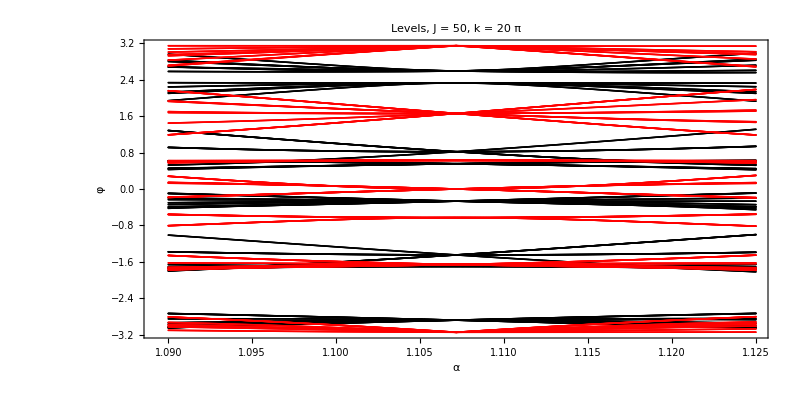

```mathematica
test
```

```mathematica
Export["levels5_J_"<>ToString[J]<>"_.png",test]
```

levels5_J_500_.png

```mathematica
(* ── Parameters ── *)
k = J * Pi * (2/5);
alist = Range[2.02,2.05,0.000125];
alist//Length
```

241

```mathematica
DistributeDefinitions[GetQKTParityEigensystem, J, k, alist];
(* ── Parallelized diagonalization over alpha ── *)
resultsphi = ParallelTable[
  Module[{data, eigenvalM, eigenvalm},
    data = GetQKTParityEigensystem[J, a, k];
    {eigenvalM, eigenvalm} = {data["Even", "Quasienergies"], data["Odd", "Quasienergies"]};
    {Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}],
     Transpose[{ConstantArray[a, Length[eigenvalm]], Arg[eigenvalm]}]}
  ],
  {a, alist},
  Method -> "CoarsestGrained"
];
```

```mathematica
{levelsM, levelsm} = Transpose[resultsphi];

test=ListPlot[
  {Flatten[levelsm, 1], Flatten[levelsM, 1]},
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k = ", NumberForm[k, {4,2}]}], 25, Black],
  AspectRatio -> 0.5, ImageSize -> 800,
  PlotRange -> All
];
```

```mathematica
test
```

-Graphics-

```mathematica
test
```

-Graphics-

```mathematica
Export["levels5b_J_"<>ToString[J]<>"_.png",test]
```

levels5b_J_500_.png

# Hypothesis 1

```mathematica
(* ── Free parameters ── *)
J = 500;
alphaTest = Pi / (2 Sqrt[2.]);
k = J * Pi * (2/5.);
nMax = J;
```

```mathematica
(* ── Build full Floquet matrix ── *)
Fmat =Floqsym[J,α,k] (* your pipeline's (2J+1)-dimensional Floquet unitary *);
identity = IdentityMatrix[Length[Fmat]];
```

```mathematica
(* ── Compute ||F^n - e^{iγ}I|| minimized over γ for each n ── *)
recurrenceNorms =ParallelTable[
  Fn = MatrixPower[Fmat, n];
  gamma = Arg[Tr[Fn] / Length[Fmat]];
  {n, Norm[Fn - Exp[I gamma] * identity, "Frobenius"]},
  {n, 1, nMax}
];
```

$Aborted

n    ||F^n - e^{iγ} I||

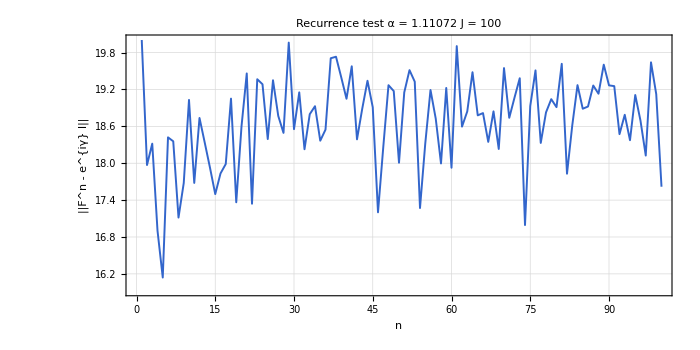

```mathematica
Print["n    ||F^n - e^{iγ} I||"];

ListPlot[recurrenceNorms,
  Joined -> True,
  PlotStyle -> Directive[RGBColor[0.2, 0.4, 0.8], PointSize[0.015], Thickness[0.002]],
  FrameLabel -> {Style["n", 18, Black], Style["||F^n - e^{iγ} I||", 18, Black]},
  PlotLabel -> Style["Recurrence test  α = " <> ToString[NumberForm[alphaTest, {6,5}]] <>
                     "  J = " <> ToString[J], 15, Black],
  Frame -> True, Axes -> False, GridLines -> Automatic,
  ImageSize -> 700, AspectRatio -> 1/2
]
```

# Hypothesis 2

```mathematica
(* ── Free parameters ── *)
J = 100;
alphaCenter = Pi / (2 Sqrt[2]);
k = J * Pi * (2/5.);
alphaRange = 0.1;
alphaStep  = 0.0005;
nTarget    =5;   (* adjust based on Hypothesis 1 output *)
```

```mathematica
(* ── Scan ── *)
alphaList = Range[alphaCenter - alphaRange, alphaCenter + alphaRange, alphaStep];

DistributeDefinitions[GetQKTParityEigensystem, J, k, alphaList, nTarget];
```

```mathematica
scanResults = ParallelTable[
  With[{Fmat = Floqsym[J,α,k]},
    With[{Fn = MatrixPower[Fmat, nTarget]},
      With[{gamma = Arg[Tr[Fn] / Length[Fmat]]},
        {a, Norm[Fn - Exp[I gamma] * IdentityMatrix[Length[Fmat]], "Frobenius"]}
      ]
    ]
  ],
  {a, alphaList},
  Method -> "CoarsestGrained"
];
```

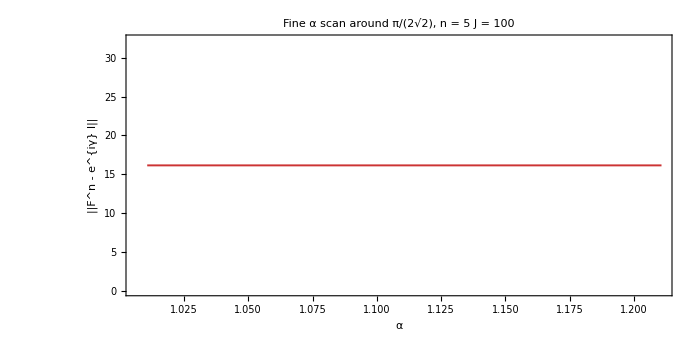

```mathematica
ListPlot[scanResults,
  Joined -> True,
  PlotStyle -> Directive[RGBColor[0.8, 0.2, 0.2], Thickness[0.002]],
  FrameLabel -> {Style["α", 18, Black], Style["||F^n - e^{iγ} I||", 18, Black]},
  PlotLabel -> Style["Fine α scan around π/(2√2),  n = " <> ToString[nTarget] <>
                     "  J = " <> ToString[J], 15, Black],
  Frame -> True, Axes -> False,
  GridLines -> {{{alphaCenter, Directive[Red, Dashed]}}, None},
  ImageSize -> 700, AspectRatio -> 1/2
]
```

# Hypothesis 4

```mathematica
(* ── Free parameters ── *)
J = 50;
alphaTest = Pi / (2 Sqrt[2]);
k = J * Pi * (2/5.);
rotOrders = Range[100];
```

```mathematica
(* ── Operators ── *)
Fmat = Floq[J,α,k];
Jz   = DiagonalMatrix[Range[J, -J, -1]];
```

```mathematica
(* ── Commutator norms ── *)
commutatorResults = Table[
  Rn       = MatrixExp[-I (2 Pi / n) Jz];
  commNorm = Norm[Fmat . Rn - Rn . Fmat, "Frobenius"];
  {n, commNorm},
  {n, rotOrders}
];
```

Rotation order n    ||[F, Rn]||

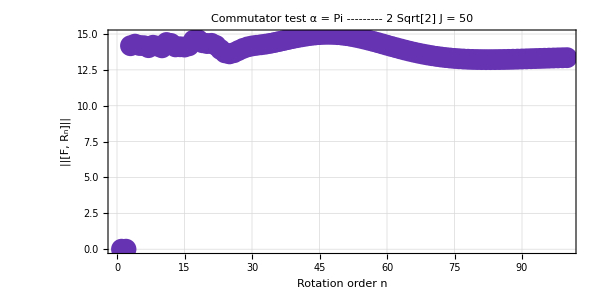

```mathematica
Print["Rotation order n    ||[F, Rn]||"];

ListPlot[commutatorResults,
  PlotStyle -> Directive[RGBColor[0.4, 0.2, 0.7], PointSize[0.025]],
  FrameLabel -> {Style["Rotation order n", 18, Black], Style["||[F, Rₙ]||", 18, Black]},
  PlotLabel -> Style["Commutator test  α = " <> ToString[NumberForm[alphaTest, {6,5}]] <>
                     "  J = " <> ToString[J], 15, Black],
  Frame -> True, Axes -> False, GridLines -> Automatic,
  ImageSize -> 600, AspectRatio -> 0.5]
```

```mathematica
(* ── Free parameters ── *)
alphaObs1 = 1.11;
alphaObs2 = 2.02;

(* ── Generate candidate expressions ── *)
candidates = DeleteDuplicates @ SortBy[Flatten @ {
  Table[Pi * p/q,       {p, 1, 6},  {q, 2, 15}],
  Table[Pi / Sqrt[n],   {n, 2, 15}],
  Table[Pi / (p + 1/q), {p, 1, 4},  {q, 2, 8}],
  Table[2 Pi * p/q,     {p, 1, 5},  {q, 5, 20}],
  Table[ArcCos[p/q],    {p, 0, 5},  {q, 2, 10}],
  Table[ArcTan[p/q],    {p, 1, 6},  {q, 1, 6}]
}, N[#] &];

(* ── Rank by proximity ── *)
ranked1 = SortBy[{N[#], Abs[N[#] - alphaObs1]} & /@ candidates, Last];
ranked2 = SortBy[{N[#], Abs[N[#] - alphaObs2]} & /@ candidates, Last];

Print["=== Top 10 candidates for α₁ ≈ ", alphaObs1, " ==="];
Print[TableForm[Take[ranked1, 10], TableHeadings -> {None, {"Value", "|residual|"}}]];

Print["=== Top 10 candidates for α₂ ≈ ", alphaObs2, " ==="];
Print[TableForm[Take[ranked2, 10], TableHeadings -> {None, {"Value", "|residual|"}}]];

(* ── Arithmetic relations between the two values ── *)
Print["\nDiagnostic ratios:"];
Print["α₂ / α₁          = ", N[alphaObs2 / alphaObs1, 10]];
Print["α₁ + α₂          = ", N[alphaObs1 + alphaObs2, 10]];
Print["2π - (α₁ + α₂)   = ", N[2 Pi - alphaObs1 - alphaObs2, 10]];
Print["π - α₁            = ", N[Pi - alphaObs1, 10]];
Print["π - α₂            = ", N[Pi - alphaObs2, 10]];
Print["α₂ - α₁           = ", N[alphaObs2 - alphaObs1, 10]];
```

=== Top 10 candidates for α₁ ≈ 1.11 ===

Value | |residual|
1.11024 | 0.000242335
1.11072 | 0.000720735
1.1088 | 0.00120259
1.10715 | 0.00285128
1.122 | 0.0119974
1.12789 | 0.0178853
1.1424 | 0.0323973
1.15928 | 0.0492795
1.0472 | 0.0628024
1.1781 | 0.0680972

=== Top 10 candidates for α₂ ≈ 2.02 ===

Value | |residual|
1.9635 | 0.0565046
2.0944 | 0.0743951
1.93329 | 0.0867122
1.88496 | 0.135044
1.848 | 0.172004
2.22144 | 0.201441
1.8138 | 0.206201
2.24399 | 0.223995
1.7952 | 0.224804
2.28479 | 0.264795

Diagnostic ratios:

α₂ / α₁          = 1.81982

α₁ + α₂          = 3.13

2π - (α₁ + α₂)   = 3.15319

π - α₁            = 2.03159

π - α₂            = 1.12159

α₂ - α₁           = 0.91